```mathematica
sf=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n.wdx"];
ft1=Query[1,1]@sf;
ft2=Query[2,1]@sf;
gt1=Query[1,2]@sf;
gt2=Query[2,2]@sf;
fp1=Interpolation[Flatten[ft1,1]];
fp2=Interpolation[Flatten[ft2,1]];
gp1=Interpolation[Flatten[gt1,1]];
gp2=Interpolation[Flatten[gt2,1]];
```

```mathematica
rfp1[x_,t_]=0.5*0.05888785346404517*x*fp1[x,t];
rfp2[x_,t_]=0.5*0.05888785346404517*x*fp2[x,t];
rgp1[x_,t_]=0.5*0.05888785346404517*x*gp1[x,t];
rgp2[x_,t_]=0.5*0.05888785346404517*x*gp2[x,t];
```

```mathematica
pf=Show[Plot3D[rfp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[rfp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t(GeV^2)","yf_(π^+ n)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

```mathematica
pg=Show[Plot3D[rgp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[rgp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t(GeV^2)","yg_(π^+ n)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-a-0.1.pdf"}];
pathg=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-a-0.1.pdf"}];
```

```mathematica
Export[pathf,pf]
Export[pathg,pg]
```

G:\calc-online\gpd\3dre\f-a-0.1.pdf

G:\calc-online\gpd\3dre\g-a-0.1.pdf

```mathematica
rfp11[x_,t_]=0.5*0.05888785346404517*x*fp1[x,-t];
rfp21[x_,t_]=0.5*0.05888785346404517*x*fp2[x,-t];
rgp11[x_,t_]=0.5*0.05888785346404517*x*gp1[x,-t];
rgp21[x_,t_]=0.5*0.05888785346404517*x*gp2[x,-t];
```

```mathematica
pf1=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1}],Plot3D[rfp21[x,t],{x,0.1,1},{t,0.03562509090909091,1}],AxesLabel->{"y","-t(GeV^2)","yf_(π^+ n)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
pg1=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.03562509090909091,1}],AxesLabel->{"y","-t(GeV^2)","yg_(π^+ n)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathf1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-a-fan.pdf"}];
pathg1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-a-fan.pdf"}];
```

```mathematica
Export[pathf1,pf1]
Export[pathg1,pg1]
```

G:\calc-online\gpd\3dre\f-a-fan.pdf

G:\calc-online\gpd\3dre\g-a-fan.pdf

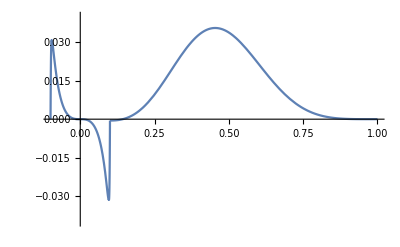

```mathematica
Show[Plot[rfp1[x,-1],{x,-0.1,0.1},PlotRange->{{-0.1,1},{-0.04,0.04}}],Plot[rfp2[x,-1],{x,0.1,1}]]
```

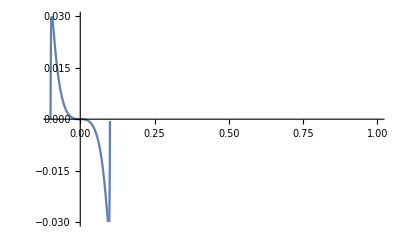

```mathematica
Plot[rfp1[x,-1],{x,-0.1,0.1},PlotRange->{{-0.1,1},{-0.03,0.03}}]
```

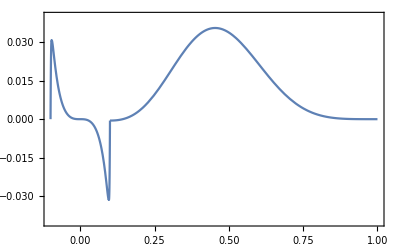
-Graphics-yyf_(π^+ n)(y)

```mathematica
pf2d=Labeled[Show[Plot[rfp1[x,-1],{x,-0.1,0.1},PlotRange->{{-0.1,1},{-0.04,0.04}}],Plot[rfp2[x,-1],{x,0.1,1}],Frame->True,FrameStyle->Directive[Thick,20]],{"y","yf_(π^+ n)(y)"},{Bottom,Left},LabelStyle->Directive[Thick,Black,16]]
```

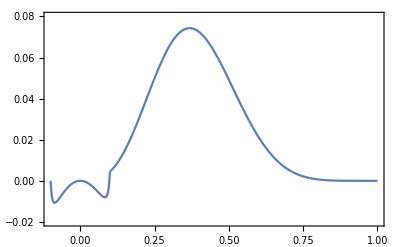
-Graphics-yyg_(π^+ n)(y)

```mathematica
pg2d=Labeled[Show[Plot[rgp1[x,-1],{x,-0.1,0.1},PlotRange->{{-0.1,1},{-0.02,0.08}}],Plot[rgp2[x,-1],{x,0.1,1}],Frame->True,FrameStyle->Directive[Thick,20]],{"y","yg_(π^+ n)(y)"},{Bottom,Left},LabelStyle->Directive[Thick,Black,16]]
```

```mathematica
pathf2d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-a-2d.png"}];
pathg2d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-a-2d.png"}];
```

```mathematica
Export[pathf2d,pf2d]
Export[pathg2d,pg2d]
```

G:\calc-online\gpd\3dre\f-a-2d.png

G:\calc-online\gpd\3dre\g-a-2d.png

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1}],Plot3D[rfp21[x,t],{x,0.1,1},{t,0.03562509090909091,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["-t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["yf_(π^+ n)(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.03562509090909091,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["-t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["yg_(π^+ n)(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"fn-a.pdf"}];
pathgn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"gn-a.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\calc-online\gpd\3dre\fn-a.pdf

G:\calc-online\gpd\3dre\gn-a.pdf